# Математическое моделирование и сложные процессы.

## Лабораторная работа №1 Моделирование поведения толпы методом конечных автоматов.

Лицкевич В.Л.

# Задание

Задача: Задан тоннель. Ширина 21 клетка на входе и 7 клеток на выходе. В тоннель прибывают люди со скоростью 11 чел за такт. Каждый человек стремится к выходу из тоннеля. Каждый человек видит ситуацию на 3 клетки в каждую сторону.
Весовые коэффициенты предпочтения движения в данном направлении определяются в зависимотсти от колличества свободных клеток ({0} | {1} | {2} | {3}
0. | 0.5 | 0.75 | 1.), и в зависимости от выгодности направления движения по следующим формулам:

```mathematica
(*Тенденция движения:{N,E,S,W} d-дирекционный синус:N=(d^2+1/3)/If[d<0,1,3,1];
E=1-d^2;
S=(d^2+1/3)/If[d>0,1,3,1];
W=((d^2+1/3))/6;*)
```

Решение о передвижении в направлениях {N,E,S,W} принимается случайным образом,на основе препочтений каждого участника численного эксперимента.

Задание 1. Построить симуляционную модель, провести возможные оптимизации. Сделать анимацию процесса продолжительностью в 100 тактов.

Задание 2. Запрограммировать численный эксперимент длинной в 1000 тактов. Построить графики колличества вошедших и вышедших за такт. (Ширина сужения 7 клеток)

Задание 3. Провести численный эксперимент для всех сужений от 0 до 15 клеток шириной, и выяснить оптимальную ширину сужения тоннеля относительно предотвращения образования пробок.

```mathematica
Tunnel[length_,constriction_]:=Module[{InW=21, OutW=7,T,TrT,i},
T=Table[0,{i,1,InW},{j,1,length}];
T⟦1⟧=T⟦-1⟧=Table[1,{i,1,length}];
TrT=Transpose@T;
TrT⟦1⟧=Table[1,{i,1,InW}];
For[i=1,i≤15-constriction,
TrT⟦-i,1;;OutW⟧=TrT⟦-i,InW-OutW+1;;InW⟧=1;i++];
For[i=15-OutW+1,i≤15,
TrT⟦-i,1;;OutW-(i-OutW-2)⟧=TrT⟦-i,InW-OutW+1+(i-OutW-2);;InW⟧=1;i++];
Transpose@TrT]
DisplayTunnel[Tunnel_]:=Graphics[Table[Which[Tunnel⟦j,i⟧==0,{EdgeForm[Thick],White,Rectangle[{i,22-j}]}, Tunnel⟦j,i⟧==1,{EdgeForm[Thick],Orange,Rectangle[{i,22-j}]}, Tunnel⟦j,i⟧==2,{EdgeForm[Thick],Red,Rectangle[{i,22-j}]}],{i,1,Length@Tunnel⟦1⟧}, {j,1,Length@Tunnel}]]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

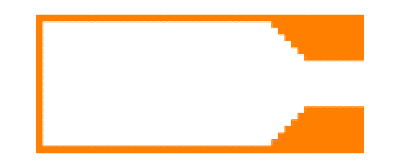

```mathematica
T=Tunnel[50,7]
DisplayTunnel[T]
```

```mathematica
Arr[Tunnel_]:=Module[{F, T=Tunnel,Em,New,i},
F= T⟦;;,2⟧;
Em=DeleteCases[Table[If[F⟦i⟧==0,i],{i,1,Length@F}],Null];
New = If[Length@Em≥11,RandomSample[Em,11],Em];
For[i=1,i≤Length@New,
	T⟦New⟦i⟧,2⟧=2;
	i++];
T
]
```

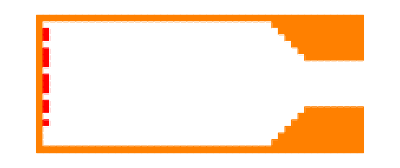

```mathematica
DisplayTunnel[T=Arr@T]
```

```mathematica
CheckWay[Tunnel_,{i_,j_},way_]:=Module[{w,n},
Which[
way=="N",
w=Quiet@Table[Check[T⟦i-k,j⟧,1],{k,1,3}],
way=="E",
w=Quiet@Table[Check[T⟦i,j+k⟧,1],{k,1,3}],
way=="S",
w=Quiet@Table[Check[T⟦i+k,j⟧,1],{k,1,3}],
way=="W",
w=Quiet@Table[Check[T⟦i,j-k⟧,1],{k,1,3}];
];
Which[
w⟦1⟧≠0,
w⟦2⟧=1;
w⟦3⟧=1,
w⟦2⟧≠0,
w⟦3⟧=1
];
n=Length@Select[w,#==0&];
Which[n==3,
1,
n==2,
0.75,
n==1,
0.5,
n==0,
0]
]
```

```mathematica
Move[Tunnel_,{i_,j_}]:=Module[{d,Nn,Ee,Ss,Ww,NN,EE,SS,WW,NESW, Step,T=Tunnel},
d = Sin@VectorAngle[{Dimensions[T]⟦2⟧,i}-{1,i},{Dimensions[T]⟦2⟧,11}-{j,i}];
d=If[j>11,d,-d];
Nn=(d^2+1/3)/If[d<0,1,3,1];
Ee=1-d^2;
Ss=(d^2+1/3)/If[d>0,1,3,1];
Ww=((d^2+1/3))/6;

NN=CheckWay[T,{i,j},"N"];
EE=CheckWay[T,{i,j},"E"];
SS=CheckWay[T,{i,j},"S"];
WW=CheckWay[T,{i,j},"W"];

NESW={Nn NN,Ee EE, Ss SS, Ww WW};
If[NESW≠{0,0,0,0},
Step = RandomChoice[NESW->{"N","E","S","W"}];
Which[
Step=="N",
T⟦i,j⟧=0;
T⟦i-1,j⟧=2,
Step=="E",
T⟦i,j⟧=0;
T⟦i,j+1⟧=2,
Step=="S",
T⟦i,j⟧=0;
T⟦i+1,j⟧=2,
Step=="W",
T⟦i,j⟧=0;
T⟦i,j-1⟧=2
]
];
{T,NESW//N,Step}
]
```

```mathematica
(*T⟦11,3⟧=2;
DisplayTunnel@T
DisplayTunnel[Move[T,{11,3}]⟦1⟧]*)
```

```mathematica
MoveColum[Tunnel_,colum_]:=Module[{T=Tunnel,CarsInColum,car,NESW,Step,V={}},
CarsInColum=DeleteCases[Table[If[T⟦i,colum⟧==2,{i,colum}],{i,2,20}],Null];
While[Length@CarsInColum≠0,
car = RandomChoice[CarsInColum];
{T,NESW,Step}=Move[T,car];
AppendTo[V,{car,NESW,Step}];
CarsInColum=Delete[CarsInColum,Position[CarsInColum,car]]
];
{T,V}
]
```

```mathematica
(*n=8;
DisplayTunnel@T
{T,V}=MoveColum[T,n];
DisplayTunnel[T]
V
Length@Select[Flatten@T,#==2&]*)
```

```mathematica
MoveTunell[Tunnel_]:=Module[{i,T=Tunnel},
For[i=Length@T,i>0,
T=MoveColum[T,i]⟦1⟧;
i--];
T]
```

```mathematica
G=Table[DisplayTunnel[T=Arr[MoveTunell[T]]],{i,1,50}];
```

```mathematica
ListAnimate[Table[G⟦i⟧,{i,1,50}]]
```